# Rolling down. Starter code

#### Let say you get a list of point from the “Coordinates tool”

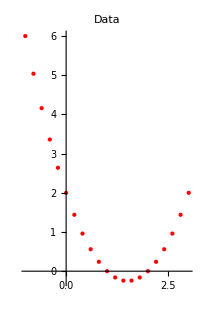

```mathematica
a=Table[{i,i^2-3 i+2+0.0*Random[]},{i,-1,3,0.2}]; (* generating a list of point to be used as an example *)
p1 =ListPlot[a,  AspectRatio->Automatic, PlotStyle->{PointSize[Medium], Red}, ImageSize->200, PlotLabel -> "Data"]
```

#### Do interpolation

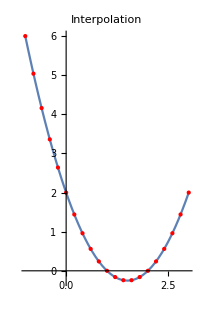

```mathematica
b=Interpolation[a]; (** b now is a function of x**)
p2 =Show[Plot[b[x],{x,-1,3}], ListPlot[a, PlotStyle->{PointSize[Medium], Red}], AspectRatio->Automatic, ImageSize->200, PlotLabel -> "Interpolation"]
```

#### Find angle of curve

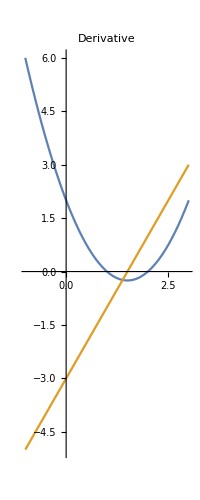

```mathematica
Der=b'; (** derivative, or tan(α) **)
p3 = Plot[{b[x],Der[x]},{x,-1,3}, AspectRatio->Automatic, ImageSize->200, PlotLabel -> "Derivative"]
```

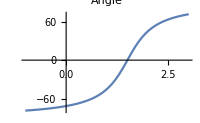

```mathematica
angle [x_]:=ArcTan[Der[x]]/Degree;
p4 = Plot[angle[x],{x,-1,3}, ImageSize->200, PlotLabel -> "Angle"]
```

#### Equations

Write and solve system of equations. Solve it using NDSolve

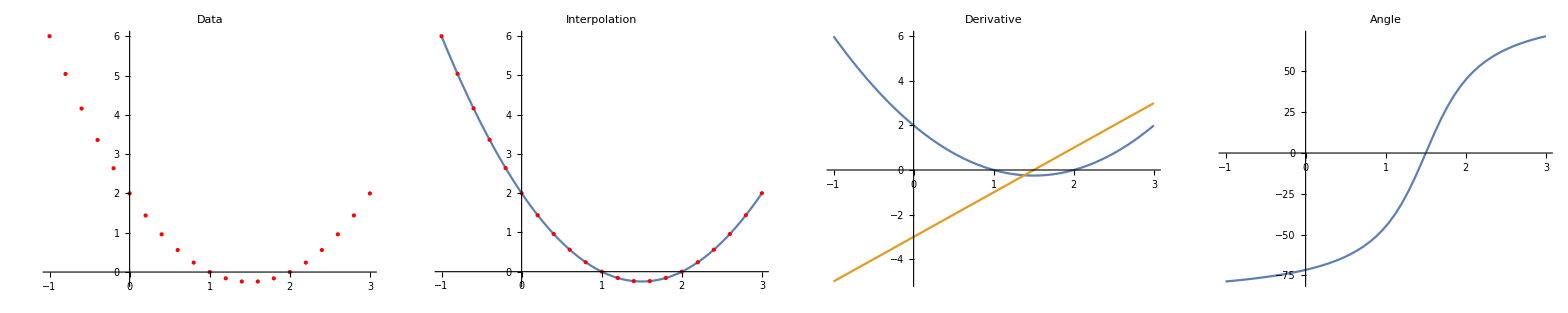

```mathematica
SetDirectory[NotebookDirectory[]];
ptotal = Deploy@Grid[{{p1,p2, p3, p4}},Dividers->Gray,Spacings->{2,2}]
Export["rolling_down_general.eps",%];
```